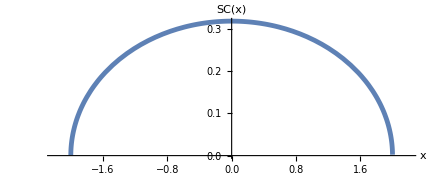

```mathematica
Plot[Sqrt[4-x^2]/2/Pi,{x,-2.2,2.2},AxesLabel->{x,SC[x]},AspectRatio->1/2.5,PlotStyle->Thickness[.008]]
```

```mathematica
nn:=5000
```

```mathematica
Monitor[Table[RandomVariate[NormalDistribution[0,1]],{i,1,nn},{j,1,nn}];,i]
```

```mathematica
A:=%48
```

```mathematica
(A+Transpose[A])/Sqrt[2];
```

```mathematica
Eigenvalues[%53];
```

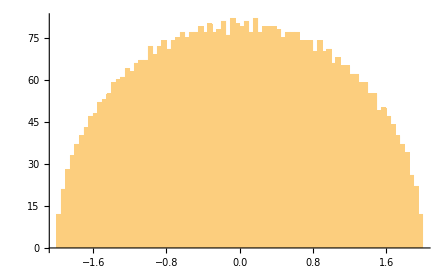

```mathematica
Histogram[%56/Sqrt[5000],70]
```